```mathematica
(* What is the area of the region in the first quadrant enclosed by the following curves:y=sin(2x) and y=arcsin(x)? *)
expr1 =Sin[2x]
expr2=ArcSin[x]
```

Sin[2 x]

ArcSin[x]

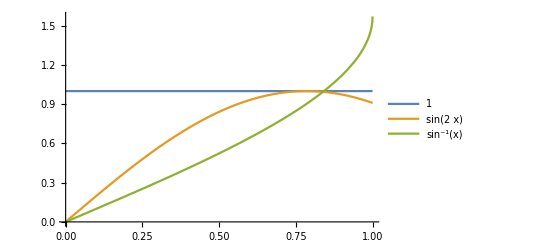

```mathematica
p=Plot[{1,Sin[2x], ArcSin[x]},{x,0,1}, PlotLegends->"Expressions"]
```

```mathematica
Export["/Users/mauro/projects/Mathematica/exprs.png", p]
```

/Users/mauro/projects/Mathematica/exprs.png

```mathematica
(* Confirm we're in the first quadrant *)
Maximize[{expr1 , 0≤ x≤1},x]
```

{1,{x→π/4}}

```mathematica
(* Find the root numerically: *)
FindRoot[expr1==expr2, {x, π/4,1}]
```

{x→0.838422}

```mathematica
(* Integrate the difference: *)NumberForm[∫_0^(x/.FindRoot[expr1==expr2, {x, π/4,1}]) (expr1-expr2) ⅆx,16]
```

0.1741916234354133